```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
SetDirectory@NotebookDirectory[];
<<MaTeX`
```

```mathematica
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
HideText[x_]:=(Print[x];AutoCollapse[]);
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,nicefrac,esint,siunitx,bm,ctex}"},"Magnification"->1.5];
MyTeX[x_]:=HideText[MaTeX[x]];
HideText["* Some Basic setup *"]
```

* Some Basic setup *

```mathematica
Clear[temp];
heatEq=D[temp[x,t],t]==D[temp[x,t],{x,2}];
ic=temp[x, 0] ==DiracDelta[x];
bc={Derivative[1,0][temp][0, t]==0,Derivative[1,0][temp][1, t]==0};
sol=DSolve[{heatEq,ic,bc},temp[x,t],{x,t}]
```

{{temp[x,t]→HeavisideTheta[0]+2 ⅇ^(-π^2 t K[1]^2) Cos[π x K[1]] HeavisideTheta[0]K[1]1∞}}

```mathematica
temp[x,t]/.sol[[1]]/.{HeavisideTheta[0]->1,K[1]->n}
```

1+2 ⅇ^(-n^2 π^2 t) Cos[n π x]n1∞

```mathematica
tempSol=temp[x,t]/.sol[[1]]/.{HeavisideTheta[0]->1,K[1]->n}//Activate//FullSimplify
```

EllipticTheta[3,(π x)/2,ⅇ^(-π^2 t)]

```mathematica
(*Plot3D[Evaluate[tempSol],{x,0,1},{t,0,.5},PlotRange->{0,3},AxesLabel->Automatic]*)
```

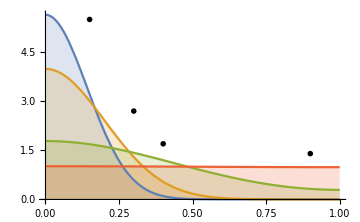

```mathematica
tvalues={.01,.02,.1,.5};
Plot[Evaluate[Table[tempSol, {t, tvalues}]], {x,0,1},
PlotRange->All,
Filling->Axis,
ImageSize->Medium,
AxesLabel->{MaTeX["x",Magnification->1.6],
MaTeX["T(x,t)",Magnification->1.3]},
PlotLabels->Placed[Table[MaTeX["\\tau="<>ToString[N[t]],Magnification->1.3], {t, tvalues}],{{.15,5.5},{.3,2.7},{.4,1.7},{.9,1.4}}]]
Export["heatConducting.pdf",%];
```

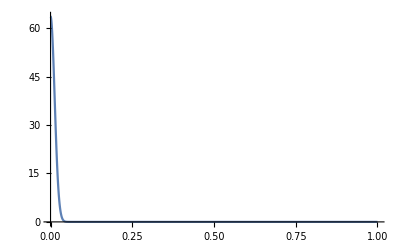

```mathematica
Plot[PDF[HalfNormalDistribution[a],x]/.{a->100},{x,0,1},PlotRange->All,
AxesLabel->{MaTeX["x",Magnification->1.6],
MaTeX["T(x,0)",Magnification->1.3]}]
Export["initCondition.pdf",%];
```

NDSolve::femcscd: PDE 以传送主导，并且结果可能不稳定. 添加人工扩散可能有帮助.

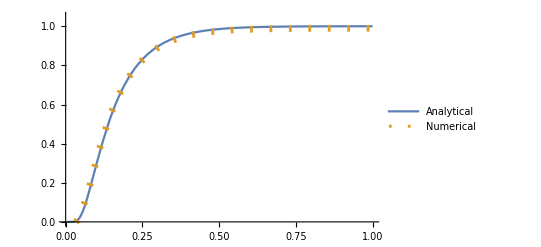

```mathematica
Clear[temp];
heatEqRef=D[temp[x,t],t]-D[temp[x,t],{x,2}]==(-NeumannValue[h temp[x,t],x==0]-NeumannValue[h temp[x,t],x==1])/.{h->0};
icRef=temp[x, 0] ==PDF[HalfNormalDistribution[a],x]/.{a->55};
solRef=NDSolve[{heatEqRef,icRef},temp,
{x,t}∈ImplicitRegion[0≤x≤1&&0≤t≤1,{x,t}]];
Plot[{tempSol/.{x->1},Evaluate[temp[x,t]/.solRef[[1]]/.{x->1}]},{t,0,1},PlotRange->{0,1.05},
PlotStyle->{Automatic,Directive[Dashing[{.005,.03}],Thickness[.012]]},
PlotLegends->{"Analytical","Numerical"},
AxesLabel->{MaTeX["\\tau",Magnification->1.5],
MaTeX["T(1,t)",Magnification->1.3]}]
Export["numericComp.pdf",%];
(*Plot[(tempSol/.{x->1})-Evaluate[temp[x,t]/.solRef[[1]]/.{x->1}],{t,0,1},PlotRange->{-.03,.03}]*)
(*Plot3D[Evaluate[temp[x,t]/.solRef[[1]]],{x,0,1},{t,0,.5},PlotRange->{-.1,3},AxesLabel->Automatic]*)
```

NDSolve::femcscd: PDE 以传送主导，并且结果可能不稳定. 添加人工扩散可能有帮助.

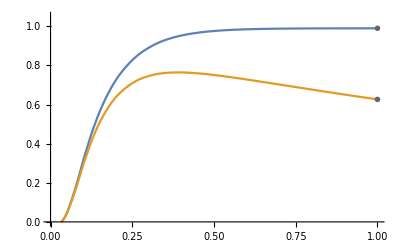

```mathematica
Clear[temp];
h0=.2;
legends=MaTeX[#,Magnification->1.2]&/@{"h=0","h="<>ToString[h0]};
heatEqMod=D[temp[x,t],t]-D[temp[x,t],{x,2}]==(-NeumannValue[h temp[x,t],x==0]-NeumannValue[h temp[x,t],x==1])/.{h->h0};
icMod=temp[x, 0] ==PDF[HalfNormalDistribution[a],x]/.{a->55};
solMod=NDSolve[{heatEqMod,icMod},temp[x,t],{x,t}∈ImplicitRegion[0≤x≤1&&0≤t≤1,{x,t}]];
Plot[
{Evaluate[temp[x,t]/.solRef[[1]]/.{x->1}],Evaluate[temp[x,t]/.solMod[[1]]/.{x->1}]},
{t,0,1},PlotRange->{0,1.05},PlotLabels->legends,
AxesLabel->{MaTeX["\\tau",Magnification->1.5],
MaTeX["T(1,t)",Magnification->1.3]}]
Export["solWithLoss.pdf",%];
```

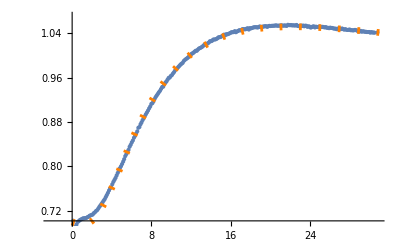

```mathematica
dat=Import["data/2.4.dat"]⟦2;;⟧;
Show[ListPlot[dat,PlotRange->{.7,1.07},
AxesLabel->{MaTeX["t / \\si{\\s}",Magnification->1.5],
MaTeX["T(h,t)\\,/\\,\\si{\\kelvin}",Magnification->1.3]}],
Plot[.7+.46Evaluate[temp[x,t]/.solMod[[1]]/.{x->1,t->t/57}],{t,0,31},
PlotStyle->Directive[Orange,Dashing[{.005,.03}],Thickness[.012]]]]
Export["datFit.pdf",%];
```

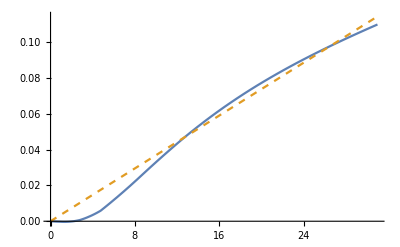

```mathematica
heatLossCorrection:=.46(Evaluate[temp[x,t]/.solRef[[1]]/.{x->1,t->t/57}]
-Evaluate[temp[x,t]/.solMod[[1]]/.{x->1,t->t/57}]);
lossFit=NonlinearModelFit[Table[{t,heatLossCorrection},{t,.1,30,.2}],k t,{k},t];
Plot[{heatLossCorrection,lossFit[t]},{t,0,31},PlotStyle->{Automatic,Dashed},
AxesLabel->{MaTeX["t / \\si{\\s}",Magnification->1.5],
MaTeX["T(h,t)\\,/\\,\\si{\\kelvin}",Magnification->1.3]}]
Export["linearCorrection.pdf",%];
```

```mathematica
Correlation@@(Table[{t,heatLossCorrection},{t,.1,30,.2}]ᵀ)
```

0.994854

```mathematica
k1Data=Import["data.xlsx"]⟦1⟧⟦Range[35,40],{1,2}⟧;
Correlation@@(k1Dataᵀ)
LinearModelFit[k1Data,x,x]["BestFitParameters"]⟦2⟧
```

-0.993278

-0.00158452

```mathematica
k2Data=Import["data.xlsx"]⟦1⟧⟦Range[43,48],{1,2}⟧;
Correlation@@(k2Dataᵀ)
LinearModelFit[k2Data,x,x]["BestFitParameters"]⟦2⟧
```

-0.997368

-0.00103379